DateLong

# Plate Layouter

## Generate print layout for paper-based microarrays

## Section.SETUP

[ What's it about ]

## All lengths are in mm

Functions

```mathematica
PickArrayFunction[arr_]:=
Function[{p},
c=If[ArrayDepth[p]>0,p,{Mod[p,wellArraySize[[2]],1],Floor[(p-1)/wellArraySize[[2]]]+1}];
Which[
!ListQ[arr],
arr,
!ListQ[arr[[c[[1]]]]],
arr[[c[[1]]]],
Length[arr[[1]]]==1,
arr[[c[[2]]]],
True,
arr[[c[[1]],c[[2]]]]
]];
```

```mathematica
n90[v_]:=Normalize[mat90.v]
```

```mathematica
mat90=RotationMatrix[π/2];
```

```mathematica
toPP[p_,c_]:=(p+platePadding)-(plateSize+2*platePadding)/2+c;
```

```mathematica
LengthArrow[x_,y_,dist_,textPos_:0.5]:=Module[
{arrowNodgeSize=1,textSeperation=2,o},
o=n90[x-y];
{
Thin,
Line[{x+o*arrowNodgeSize+o*dist,x-o*arrowNodgeSize+o*dist}],
Line[{y+o*arrowNodgeSize+o*dist,y-o*arrowNodgeSize+o*dist}],
Arrowheads[{-1,1}*0.01],
Arrow[{x+o*dist,y+o*dist}],
Text[Style[ToString[NumberForm[Norm[x-y]*1.,{5,2}]],FontFamily->"Gill Sans Light",FontSize->fontSize,Background->Directive[White,Opacity[0.8]]],y+textPos*(x-y)+o*(dist+textSeperation),Center,Normalize[y-x]]
}
]
```

Settings

```mathematica
inch=25.4;
dpi=72/inch;
```

```mathematica
div=2;
wellSpacing=9/div;
wellArraySize={12,8}*div;
```

```mathematica
div=4;
wellSpacing=9/div;
wellArraySize={12,8}*div;
```

```mathematica
div=1;
wellSpacing=9/div;
wellArraySize={12,8}*div;
```

```mathematica
wellDiameter=7;
plateSize={127.66,85.48};
plateIndent=2;
fontSize=Scaled[0.015];
wellLineThickness=0.5;
platePadding=20;
cutLinePadding=4;
leftNodgeSize=6;
gridThickness=0.25;
numberingSteps=1;
holderIndent=0.74;
rightInShift=4.09;
paperSize={200,200};
placements={1,2};
rotation=False;
wellSeperation=0.5;
paperGrabOutlet=15.91;
wellPlatePadding=0.2;
markingsOffset={15,6};
```

```mathematica
pl:={plateIndent+holderIndent-paperGrabOutlet,plateIndent+holderIndent,plateSize[[1]]-plateIndent-holderIndent-rightInShift,plateSize[[2]]-plateIndent-holderIndent};
actualCuttedPaperSize:={pl[[3]]-pl[[1]],pl[[4]]-pl[[2]]};
```

```mathematica
actualCuttedPaperSize
```

{134.,80.}

Markings

```mathematica
markSquareSize=5;
markLineLength=15;
markLineThickness=0.5;
markSize=200-2*10;
```

```mathematica
Markings[p_]:=
Module[{},
leftTop=p;
{
White,
Rectangle[leftTop-markLineThickness/2*{1,-1},leftTop+(markLineLength+markLineThickness/2)*{1,-1}],
Rectangle[leftTop-markSize*{0,1}+markLineLength*{1,0},leftTop-markSize*{0,1}+markLineLength*{0,1}],
Rectangle[leftTop+markSize*{1,0}+markLineLength*{-1,0},leftTop+markSize*{1,0}+markLineLength*{0,-1}],
Black,
CapForm["Square"],EdgeForm[None],
Rectangle[leftTop-markLineThickness/2*{1,-1},leftTop+(markSquareSize+markLineThickness/2)*{1,-1}],
Black,AbsoluteThickness[markLineThickness dpi],
Line[{leftTop-markSize*{0,1}+markLineLength*{1,0},leftTop-markSize*{0,1},leftTop-markSize*{0,1}+markLineLength*{0,1}}],
Line[{leftTop+markSize*{1,0}+markLineLength*{-1,0},leftTop+markSize*{1,0},leftTop+markSize*{1,0}+markLineLength*{0,-1}}]
}
]
```

Code

```mathematica
RenderPlate[opts___]:=Module[{},
showSize=SizeLabel/.{opts}/.{SizeLabel->False};
showCuts=CutMarks/.{opts}/.{CutMarks->False};
showPlate=PlateMarks/.{opts}/.{PlateMarks->False};
wellEdgeThickness=PickArrayFunction[(WellThickness/.{opts}/.{WellThickness->wellLineThickness})];
title=Title/.{opts}/.{Title->""};
wellColor=PickArrayFunction[(WellColor/.{opts}/.{WellColor->White})];
wellEdgeColor=PickArrayFunction[((WellEdgeColor/.{opts})/.{WellEdgeColor->White})];
wellDiameter=PickArrayFunction[((WellDiameter/.{opts})/.{WellDiameter->7})];
plateBackground=PlateBackground/.{opts}/.{PlateBackground->White};
rowLabel=RowLabels/.{opts}/.{RowLabels->Map[FromCharacterCode[64+#]&,Range[wellArraySize[[2]]]]};
colLabel=ColLabels/.{opts}/.{ColLabels->Map[ToString[#]&,Range[wellArraySize[[1]]]]};
cellLabel=PickArrayFunction[(CellLabels/.{opts}/.{CellLabels->""})];
cellSymbol=PickArrayFunction[(CellSymbol/.{opts}/.{CellSymbol->Null})];
gridSize=wellArraySize*wellSpacing;
gridStart1A=(plateSize-wellArraySize*wellSpacing)/2;
wellCenter1A=(plateSize-wellArraySize*wellSpacing)/2+wellSpacing/2;
wellCenters=Flatten[
Table[wellCenter1A+wellSpacing*{x-1,y-1},{x,wellArraySize[[1]]},{y,wellArraySize[[2]],1,-1}]
,1];
gridLinesX=
Table[Line[{gridStart1A+{x*wellSpacing,0},gridStart1A+{x*wellSpacing,gridSize[[2]]}}],{x,0,wellArraySize[[1]]}];
gridLinesY=
Table[Line[{gridStart1A+{0,y*wellSpacing},gridStart1A+{gridSize[[1]],y*wellSpacing}}],{y,0,wellArraySize[[2]]}];
gr=Graphics[{
If[showPlate,
{
EdgeForm[Directive[Thin, Black]],White,
Rectangle[{0,0},plateSize,RoundingRadius->2],
Rectangle[{0,0}+plateIndent,{0,0}+plateSize-plateIndent,RoundingRadius->2],
EdgeForm[None],White,
Rectangle[{0,0}+{0,1}*plateSize-plateIndent*{-1,1}+{-0.1,0.1},{0,0}+{0,1}*plateSize-plateIndent*{-1,1}+{1,-1}*leftNodgeSize,RoundingRadius->0],
Thin,Black,
Line[{
{0,0}+{0,1}*plateSize-plateIndent*{-1,1}+{0,-1}*leftNodgeSize,
{0,0}+{0,1}*plateSize-plateIndent*{-1,1}+{1,0}*leftNodgeSize
}]
},{}],
If[showCuts,
{
Thin,White,Opacity[0],Black,Opacity[1],Dashed,
Line[{pl[[{1,2}]]+{-cutLinePadding,0},pl[[{3,2}]]+{+cutLinePadding,0}}],
Line[{pl[[{1,4}]]+{-cutLinePadding,0},pl[[{3,4}]]+{+cutLinePadding,0}}],
Line[{pl[[{1,2}]]+{0,-cutLinePadding},pl[[{1,4}]]+{0,+cutLinePadding}}],
Line[{pl[[{3,2}]]+{0,-cutLinePadding},pl[[{3,4}]]+{0,+cutLinePadding}}]
},
{}],
EdgeForm[Directive[Thin,Black]],Opacity[1],EdgeForm[None],
plateBackground,
Rectangle[wellCenters[[1]]+(wellSpacing/2+wellLineThickness/2+wellPlatePadding)*{-1,1},wellCenters[[-1]]-(wellSpacing/2+wellLineThickness/2+wellPlatePadding)*{-1,1}],
MapIndexed[{wellColor[#2[[1]]],Disk[#,wellDiameter[#2[[1]]]/2+wellEdgeThickness[#2[[1]]]/2]}&,wellCenters],
Dashing[{}],AbsoluteThickness[wellLineThickness*dpi],
MapIndexed[{wellEdgeColor[#2[[1]]],AbsoluteThickness[wellEdgeThickness[#2[[1]]]*dpi],Circle[#,wellDiameter[#2[[1]]]/2+wellEdgeThickness[#2[[1]]]/2]}&,wellCenters],
Black,
MapIndexed[{Text[Style[cellLabel[#2[[1]]],FontFamily->"Futura",FontSize->fontSize],#,{0,0}]}&,wellCenters],
MapIndexed[If[cellSymbol[#2[[1]]]=!=Null,Inset[cellSymbol[#2[[1]]],#,Center,GetSize[cellSymbol[#2[[1]]]]]]&,wellCenters],
Black,AbsoluteThickness[gridThickness*dpi],
Table[
Text[Style[rowLabel[[y]],FontFamily->"Futura",FontSize->fontSize],wellCenter1A+{-2,0}+wellSpacing*{-0.5,wellArraySize[[2]]-y}],
{y,1,wellArraySize[[2]],numberingSteps}],
Table[
Text[Style[colLabel[[x]],FontFamily->"Futura",FontSize->fontSize],wellCenter1A+{0,2}+wellSpacing*{x-1,wellArraySize[[2]]-0.5}],
{x,1,wellArraySize[[1]],numberingSteps}
],
Text[Style[title,FontFamily->"Gill Sans",FontSize->2*fontSize],{pl[[1]]+3,Mean[pl[[{2,4}]]]},{0,0},{0,1}]
,
If[showSize,
{
LengthArrow[{plateIndent+holderIndent,0},{plateSize[[1]]-(plateIndent+holderIndent)-rightInShift,0},3.0],
LengthArrow[{plateSize[[1]],plateIndent+holderIndent},{plateSize[[1]],plateSize[[2]]-(plateIndent+holderIndent)},3.0]
}]
},ImagePadding->0,PlotRange->Transpose[{{0,0}-platePadding,plateSize+platePadding}],Frame->False]
]
```

```mathematica
GeneratePaper[plate1_,plate2_]:=Module[{},Graphics[{Inset[plate1,{100,55},Center,plateSize+2*platePadding],Inset[plate2,{100,145},Center,plateSize+2*platePadding],If[False,{LengthArrow[{0,toPP[{0,0},{100,55}][[2]]},toPP[{pl[[1]],0},{100,55}],-8,0.75],LengthArrow[{toPP[{0,0},{100,55}][[1]],0},toPP[{0,pl[[2]]},{100,55}],-8],LengthArrow[{toPP[{0,0},{100,145}][[1]],0},toPP[{0,pl[[2]]},{100,145}],-25],LengthArrow[{0,toPP[{0,0},{100,55}][[2]]},toPP[{pl[[1]],0},{100,55}],-8,0.75]}]},ImagePadding->0,PlotRange->{{0,paperSize[[1]]},{0,paperSize[[2]]}},Frame->False]]
```

```mathematica
GeneratePrintFile[paper_,opts___]:=
Module[
{},
markingsOff=MarkerOffset/.{opts}/.{MarkerOffset->markingsOffset};
flip=Flip/.{opts}/.Flip->False;
showCutterMarking=CutterMark/.{opts}/.{CutterMark->True};
markingsPlace={0,200}-mat90.(toPP[pl[[{1,2}]],{100,55}]-markingsOff);
orientation=If[flip,{{0,-1},{-1,0}},{0,-1}];
oposition=If[flip,{0,paperSize[[2]]},{0,0}];
Graphics[{
Inset[paper,{0,paperSize[[2]]},oposition,paperSize,orientation],
If[showCutterMarking,
Markings[markingsPlace],
{}
]
},
Frame->False,PlotRange->{{0,paperSize[[1]]},{0,paperSize[[2]]}},ImagePadding->0,AspectRatio->1,ImageSize->800]
]
```

```mathematica
p8=RenderPlate[Title->"",WellEdgeColor->Directive[Black],WellColor->Black,ColLabels->Table["",{12}],RowLabels->Table["",{8}],CutMarks->False];
paper8=GeneratePaper[p8,p8];
out8=GeneratePrintFile[paper8,Flip->True,CutterMark->False];
Export[ToResourceFile["BlackBackArray.pdf"],out8,ImageSize->dpi*(paperSize)]
```

/Users/jan-hendrikprinz/Studium/Projekte/general/PaperPlates/resources/BlackBackArray.pdf

```mathematica
p1=RenderPlate[Title->"Color + DMSO",WellEdgeColor->{CMYKColor[0,0,0,1],CMYKColor[1,0,0,0],CMYKColor[0,1,0,0],CMYKColor[0,0,1,0],White,Black,Black,Black}];
p2=RenderPlate[Title->"Wax Fluorescence",WellEdgeColor->Directive[White],
CellLabels->{"","","","","","","",{"  0%"," 10%"," 20%"," 30%"," 40%"," 50%"," 60%"," 70%"," 80%"," 90%","100%",""}},WellColor->Transpose[Table[{CMYKColor[0,0,0,vv],CMYKColor[vv,0,0,0],CMYKColor[0,vv,0,0],CMYKColor[0,0,vv,0],CMYKColor[1,0,0,vv],CMYKColor[0,1,0,vv],CMYKColor[0,0,1,vv],White},{vv,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0,0.0}}]]];
paper1=GeneratePaper[p2,p1]
Export[ToResourceFile["pap1.eps"],GeneratePrintFile[paper1],ImageSize->dpi*(paperSize)];
```

-Graphics-

```mathematica
GeneratePrintFile[paper1]
```

-Graphics-

```mathematica
markingsPlace
```

{9.,192.}

```mathematica
actualCuttedPaperSize
```

{134.,80.}

```mathematica
paper
```

```mathematica
OpenProjectFolder[]
```

```mathematica
wellSeperation=7;
p5=RenderPlate[Title->"Calibration",
CellLabels->"",WellEdgeColor->Black,
WellColor->White,WellThickness->0.3]
wellSeperation=1;
paper2=GeneratePaper[p5,p3]
Export[ToResourceFile["calibration.pdf"],GeneratePrintFile[paper2],ImageSize->dpi*(paperSize)]
```

-Graphics-

-Graphics-

/Users/jan-hendrikprinz/Studium/Projekte/general/PaperPlates/resources/calibration.pdf

```mathematica
Table[Range[7.5,2.0,-0.5],{8}]//Dimensions
```

{8,12}

```mathematica
p3=RenderPlate[Title->"",WellEdgeColor->Black,PlateMarks->True,CutMarks->True];
wd=wellSeperation;
wellSeperation=1.5;
p4=RenderPlate[Title->"Well Line Thickness",WellEdgeColor->Black,WellThickness->Range[0.3,1.0,0.1],PlateMarks->True,CutMarks->True,WellDiameter->Table[Range[7.5,2.0,-0.5],{8}]];
wellSeperation=wd;
paper2=GeneratePaper[p4,p3]
Export[ToResourceFile["pap2.pdf"],GeneratePrintFile[paper2],ImageSize->dpi*(paperSize)]
```

-Graphics-

/Users/jan-hendrikprinz/Studium/Projekte/general/PaperPlates/resources/pap2.pdf

```mathematica
p8=RenderPlate[Title->"",WellEdgeColor->Directive[Black],WellColor->Black,ColLabels->Table["",{12}],RowLabels->Table["",{8}],CutMarks->False,WellThickness->Range[0.3,1.0,0.1],WellDiameter->Table[Range[7.5,2.0,-0.5]+1,{8}]];
paper8=GeneratePaper[p8,p8];
out8=GeneratePrintFile[paper8,Flip->True,CutterMark->False]
Export[ToResourceFile["BlackBackArray.pdf"],out8,ImageSize->dpi*(paperSize)];
```

-Graphics-

```mathematica
OpenProjectFolder[]
```

```mathematica
Export["/Users/jan-hendrikprinz/Desktop/Y.pdf",paper,ImageSize->dpi*(paperSize)];
```

```mathematica
Export["/Users/jan-hendrikprinz/Desktop/X.pdf",gr,ImageSize->dpi*(plateSize+2*platePadding)];
```

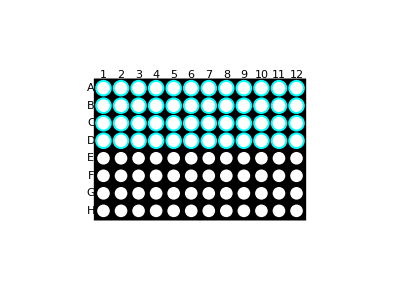

```mathematica
RenderPlate[Title->"",PlateBackground->Black,WellEdgeColor->{CMYKColor[1,0,0,0],CMYKColor[1,0,0,0],CMYKColor[1,0,0,0],CMYKColor[1,0,0,0],Black,Black,Black,Black}]
```

```mathematica
GetSize[cellSymbol[1]]
```

Part::partw: Part 2 of Transpose[All] does not exist.

-All+Transpose[All]⟦2⟧

```mathematica
crosshair=Graphics[{AbsoluteThickness[0.2 dpi],Circle[{0,0},1],Line[{{-1,0},{1,0}}*2],Line[{{0,-1},{0,1}}*2]},Frame->False,PlotRange->{{-1,1},{-1,1}}*2];
pCH=RenderPlate[Title->"",WellEdgeColor->Black,PlateMarks->False,CutMarks->True,CellSymbol->crosshair];
pYellow=RenderPlate[Title->"",WellEdgeColor->CMYKColor[0,0,1,0],WellColor->CMYKColor[0,0,1,0],ColLabels->Table["",{12}],RowLabels->Table["",{8}],CutMarks->True,WellThickness->0.0,WellDiameter->3];
paper9=GeneratePaper[pCH,pYellow];
out9=GeneratePrintFile[paper9,Flip->False,CutterMark->False]
Export[ToResourceFile["Calibration.pdf"],out9,ImageSize->dpi*(paperSize)];
```

-Graphics-

```mathematica
OpenProjectFolder[]
```

## Section.COMPUTATIONS

## Section.RESULTS

[ Summary, Conclusions & Outlook ]

## Section.BIBLIOGRAPHY

[ Literature Links, etc. ]

### Load BibTeX Files

[ Load Default Library ]

```mathematica
projectBibLibrary=LoadBibTeXLibraryFromFile[$DefaultBibTeXLibrary];
```

```mathematica
projectBibLibrary=LoadBibTeXLibraryFromFile[FileNameJoin[$literaturePath,"nameOfYourBibFileHere.bib"]];
```

## Section.APPENDIX

[ Additional Material ]